# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
```

```mathematica
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];

kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# Helpers

```mathematica
(* ================================================================ *)
(* MODULE 3: LOCAL HELPERS                                          *)
(* IntPrCOEFast interpolator + GoF metrics + collage builders      *)
(* ================================================================ *)

Print["\n=== BUILDING HELPERS ==="];
IntPrCOEFast = Interpolation[
  Table[{r, NIntegrate[PrCOE[x], {x, 0, r}]}, {r, 0, 1, 0.001}]];
Print["  IntPrCOEFast[0.5] = ", IntPrCOEFast[0.5]];

(* --- GoF metrics from sorted data --- *)
KSFromSorted[empCDF_List, theoCDFvals_List] := Max[Abs[empCDF - theoCDFvals]];

CvMFromSorted[n_Integer, theoCDFvals_List] :=
  Module[{midEmp = N[(2 Range[n] - 1) / (2 n)]},
    Total[(midEmp - theoCDFvals)^2] / n + 1 / (12 n)];

MSDFromSorted[empCDF_List, theoCDFvals_List] := Mean[(empCDF - theoCDFvals)^2];

(* --- GoF for one spectrum (pure numerical, parallelizable) --- *)
ComputeGoFSingle[specData_Association] :=
  Module[{spacings, sp, ratios, sortS, sortR, nS, nR,
          empS, empR, theoS, theoR},
    spacings = NNSpacings[specData]; sortS = Sort[spacings]; nS = Length[sortS];
    empS = N[Range[nS] / nS]; theoS = N[IntWignerCOE /@ sortS];
    sp = Differences[specData["Spectrum"]];
    ratios = Min /@ Transpose[{Most[sp] / Rest[sp], Rest[sp] / Most[sp]}];
    sortR = Sort[ratios]; nR = Length[sortR];
    empR = N[Range[nR] / nR]; theoR = N[IntPrCOEFast /@ sortR];
    {KSFromSorted[empS, theoS], CvMFromSorted[nS, theoS], MSDFromSorted[empS, theoS],
     KSFromSorted[empR, theoR], CvMFromSorted[nR, theoR], MSDFromSorted[empR, theoR]}
  ];

(* --- Extract spacings + ratios --- *)
ExtractStats[specData_Association] :=
  Module[{spacings, sp, ratios},
    spacings = NNSpacings[specData];
    sp = Differences[specData["Spectrum"]];
    ratios = Min /@ Transpose[{Most[sp] / Rest[sp], Rest[sp] / Most[sp]}];
    <|"SortedS" -> Sort[spacings], "SortedR" -> Sort[ratios]|>];

(* --- Collage row for one sector --- *)
MakeRowPlots[sortedS_List, sortedR_List, flucData_Association, label_String] :=
  Module[{nS, nR, empS, empR, theoS, theoR, ksS, ksR, diffS, diffR},
    nS = Length[sortedS]; nR = Length[sortedR];
    empS = N[Range[nS] / nS]; empR = N[Range[nR] / nR];
    theoS = N[IntWignerCOE /@ sortedS];
    theoR = N[IntPrCOEFast /@ sortedR];
    ksS = Max[Abs[empS - theoS]]; ksR = Max[Abs[empR - theoR]];
    diffS = (empS - theoS)^2; diffR = (empR - theoR)^2;
    {(* P(s) *)
     Show[Histogram[sortedS, {0, 4, 0.05}, "ProbabilityDensity",
       ChartStyle -> Directive[LightGray, EdgeForm[Gray]], PlotRange -> {{0, 3.5}, {0, 1.1}}],
      Plot[WignerCOE[x], {x, 0, 3.5}, PlotStyle -> {Red, Dashed, Thick}],
      Plot[Exp[-x], {x, 0, 3.5}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"s", "P(s)"}, PlotLabel -> label <> " P(s)", ImageSize -> $cSize],
     (* P(r) *)
     Show[Histogram[sortedR, {0, 1, 0.02}, "ProbabilityDensity",
       ChartStyle -> Directive[LightGray, EdgeForm[Gray]], PlotRange -> {{0, 1}, {0, 2.2}}],
      Plot[PrCOE[x], {x, 0, 1}, PlotStyle -> {Red, Dashed, Thick}],
      Plot[PrPoisson[x], {x, 0, 1}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"r", "P(r)"}, PlotLabel -> label <> " P(r)", ImageSize -> $cSize],
     (* I(s) *)
     Show[ListLinePlot[Transpose[{sortedS, empS}], PlotStyle -> {Blue, Thick},
       PlotRange -> {{0, 3.5}, {0, 1}}],
      Plot[IntWignerCOE[x], {x, 0, 3.5}, PlotStyle -> {Red, Dashed}],
      Plot[1 - Exp[-x], {x, 0, 3.5}, PlotStyle -> {Black, Dashed}],
      $cOpts, FrameLabel -> {"s", "I(s)"},
      PlotLabel -> label <> " I(s) KS=" <> ToString[NumberForm[ksS, 4]], ImageSize -> $cSize],
     (* I(r) *)
     Show[ListLinePlot[Transpose[{sortedR, empR}], PlotStyle -> {Blue, Thick},
       PlotRange -> {{0, 1}, {0, 1}}],
      ListLinePlot[Transpose[{sortedR, theoR}], PlotStyle -> {Red, Dashed}],
      $cOpts, FrameLabel -> {"r", "I(r)"},
      PlotLabel -> label <> " I(r) KS=" <> ToString[NumberForm[ksR, 4]], ImageSize -> $cSize],
     (* CDF diff (s) *)
     ListLinePlot[Transpose[{sortedS, diffS}], PlotStyle -> {Blue, Thick},
      Filling -> Axis, FillingStyle -> Directive[Opacity[0.3], Blue],
      $cOpts, FrameLabel -> {"s", "(I-I_COE)^2"}, PlotLabel -> label <> " CDF diff (s)",
      PlotRange -> All, ImageSize -> $cSize],
     (* CDF diff (r) *)
     ListLinePlot[Transpose[{sortedR, diffR}], PlotStyle -> {Blue, Thick},
      Filling -> Axis, FillingStyle -> Directive[Opacity[0.3], Blue],
      $cOpts, FrameLabel -> {"r", "(I-I_COE)^2"}, PlotLabel -> label <> " CDF diff (r)",
      PlotRange -> All, ImageSize -> $cSize],
     (* Fluctuation *)
     ListLinePlot[Transpose[{flucData["x"], flucData["delta"]}],
      PlotStyle -> {Blue, AbsoluteThickness[0.5]}, $cOpts,
      FrameLabel -> {"x", "\!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},
      PlotLabel -> label <> " Fluctuation", ImageSize -> $cSize,
      GridLines -> {None, {0}}, GridLinesStyle -> Directive[Red, Dashed]]}
  ];
```

=== BUILDING HELPERS ===

IntPrCOEFast[0.5] = 0.460051

# Parameters

```mathematica
(* ================================================================ *)
(* MODULE 1: PARAMETERS                                             *)
(* ================================================================ *)

J       = 1000;
alpha   = 0.84;
kCenter = 27.5;
delta   = 0.001;
nQKT    = 100;
nCOE    = 50;
Lmax    = 50;
lDomain = Join[Range[0.1, 5, 0.1], Range[5.5, Lmax, 0.5]];
tauMax  = 3.0;
nPtsSFF = 5000;

(* --- Directories --- *)
runLabel = "J" <> ToString[J] <> "_k" <> kStr[kCenter];
resultsDir = FileNameJoin[{baseDir, "Results", runLabel}];
evenDir    = FileNameJoin[{resultsDir, "Even"}];
oddDir     = FileNameJoin[{resultsDir, "Odd"}];
plotDir    = FileNameJoin[{resultsDir, "plots"}];
collageDir = FileNameJoin[{resultsDir, "individual"}];
EnsureDir[evenDir]; EnsureDir[oddDir];
EnsureDir[plotDir]; EnsureDir[collageDir];

(* --- Plot style --- *)
$pOpts = Sequence[ImageSize -> 800, Frame -> True,
  FrameStyle -> Directive[Black, 25],
  LabelStyle -> Directive[Black, 25]];
$cOpts = Sequence[Frame -> True,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]];
$cSize = 380;
$legStyle = Directive[Black, 18];

SavePlot[plt_, name_] := (
  Export[FileNameJoin[{plotDir, name <> ".png"}],
    Rasterize[plt, ImageResolution -> 150, Background -> White]];
  Print["  Saved: ", name, ".png"]);
```

# Method

```mathematica
(* --- Generate --- *)
  Print["=== GENERATING QKT ENSEMBLE ==="];
(*  SeedRandom[42];*)
  kList = RandomReal[{kCenter - delta, kCenter + delta}, nQKT];
  {tGen, qktEnsemble} = AbsoluteTiming[
    GenerateQKTEnsemble[J, alpha, kList]];
  Print["  ", nQKT, " matrices done in ", Round[tGen, 0.1], "s"];
  Export[FileNameJoin[{evenDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Even"], "WDX"];
  Export[FileNameJoin[{oddDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Odd"], "WDX"];
  Print["  Spectra exported"];
```

=== GENERATING QKT ENSEMBLE ===

100 matrices done in 2043.7s

Spectra exported

```mathematica
(* --- Import --- *)
(*qktEnsemble = <|
    "Even" -> Import[FileNameJoin[{evenDir, "spectra.wdx"}]],
    "Odd"  -> Import[FileNameJoin[{oddDir, "spectra.wdx"}]]|>;
  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];*)
  qktEnsemble = <|
    "Even" -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Even\\spectra_k27.5.wdx"],
    "Odd"  -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Odd\\spectra_k27.5.wdx"]|>;

  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];
```

Imported successfully

```mathematica
dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];
nReal = Length[qktEnsemble["Even"]];
Print["  Even N=", dimE, ", Odd N=", dimO, ", nReal=", nReal];
```

Even N=1001, Odd N=1000, nReal=100

# Individual realization

```mathematica
(* ================================================================ *)
(* MODULE 4: INDIVIDUAL REALIZATION COLLAGES                        *)
(* ================================================================ *)

Print["\n=== INDIVIDUAL COLLAGES ==="];

Do[
  Module[{stE, stO, flE, flO, colE, colO, collage},
    stE = ExtractStats[qktEnsemble["Even"][[i]]];
    stO = ExtractStats[qktEnsemble["Odd"][[i]]];
    flE = GetFluctuations[qktEnsemble["Even"][[i]]];
    flO = GetFluctuations[qktEnsemble["Odd"][[i]]];
    colE = MakeRowPlots[stE["SortedS"], stE["SortedR"], flE, "Even"];
    colO = MakeRowPlots[stO["SortedS"], stO["SortedR"], flO, "Odd"];
    collage = Grid[
      Prepend[Transpose[{colE, colO}],
        {Style["Even", Bold, 20], Style["Odd", Bold, 20]}],
      Spacings -> {1, 0.5}, Frame -> All, FrameStyle -> GrayLevel[0.85]];
    Export[FileNameJoin[{collageDir,
      "realization_" <> StringPadLeft[ToString[i], 4, "0"] <> ".png"}],
      Rasterize[collage, ImageResolution -> 150, Background -> White]];
    If[Mod[i, 50] == 0 || i == 1, Print["  Exported ", i, "/", nReal]];
  ];
, {i, nReal}];
Print["Individual collages complete"];
```

=== INDIVIDUAL COLLAGES ===

Exported 1/100

Exported 50/100

Exported 100/100

Individual collages complete

# Coe reference

```mathematica
(* ================================================================ *)
(* MODULE 6: COE REFERENCE + NUMBER VARIANCE + SFF                  *)
(* ================================================================ *)

Print["\n=== COE REFERENCE ==="];
dimCOE = dimE;
{tCOE, coeSpectra} = AbsoluteTiming[GenerateCOEEnsemble[dimCOE, nCOE]];
Print["  ", nCOE, " COE(", dimCOE, ") done in ", Round[tCOE, 0.1], "s"];

Print["Computing COE Sigma2..."];
{tS, sigma2COE} = AbsoluteTiming[EnsembleSigma2[coeSpectra, lDomain]];
Print["  Done in ", Round[tS, 0.1], "s"];

Print["Computing COE SFF..."];
{tF, sffCOE} = AbsoluteTiming[EnsembleSFF[coeSpectra, tauMax, nPtsSFF]];
Print["  Done in ", Round[tF, 0.1], "s"];
coeSpectra = .;

Print["\n=== QKT NUMBER VARIANCE ==="];
{t1, sigma2Even} = AbsoluteTiming[EnsembleSigma2[qktEnsemble["Even"], lDomain]];
{t2, sigma2Odd}  = AbsoluteTiming[EnsembleSigma2[qktEnsemble["Odd"], lDomain]];
Print["  Even: ", Round[t1, 0.1], "s, Odd: ", Round[t2, 0.1], "s"];

SavePlot[Legended[Show[
  ListLinePlot[Transpose[{sigma2COE["LValues"], sigma2COE["Sigma2TheorMean"]}], PlotStyle -> {Red, Thick}],
  ListLinePlot[Transpose[{sigma2Even["LValues"], sigma2Even["Sigma2TheorMean"]}], PlotStyle -> {Blue, Thick}],
  ListLinePlot[Transpose[{sigma2Odd["LValues"], sigma2Odd["Sigma2TheorMean"]}], PlotStyle -> {Darker[Green], Thick}],
  Plot[COEAsymptoticSigma2[L], {L, 0.5, Lmax}, PlotStyle -> {Orange, Thick, Dashed}],
  Plot[L, {L, 0.5, Lmax}, PlotStyle -> {Black, Dashed, Thin}],
  $pOpts, FrameLabel -> {"L", "\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},
  PlotLabel -> "Number Variance: J=" <> ToString[J],
  PlotRange -> {All, {0, Automatic}}],
  Placed[LineLegend[{Directive[Blue, Thick], Directive[Darker[Green], Thick],
    Directive[Red, Thick], Directive[Orange, Thick, Dashed]},
    {"Even", "Odd", "COE", "COE asym."}, LabelStyle -> $legStyle], {Right, Bottom}]
], "sigma2"];

(* Residual *)
Module[{nMin, lR, resE, resO},
  nMin = Min[Length /@ {sigma2Even["LValues"], sigma2Odd["LValues"], sigma2COE["LValues"]}];
  lR = sigma2COE["LValues"][[1 ;; nMin]];
  resE = sigma2Even["Sigma2TheorMean"][[1 ;; nMin]] - sigma2COE["Sigma2TheorMean"][[1 ;; nMin]];
  resO = sigma2Odd["Sigma2TheorMean"][[1 ;; nMin]] - sigma2COE["Sigma2TheorMean"][[1 ;; nMin]];
  SavePlot[Legended[Show[
    ListLinePlot[Transpose[{lR, resE}], PlotStyle -> {Blue, Thick}],
    ListLinePlot[Transpose[{lR, resO}], PlotStyle -> {Darker[Green], Thick}],
    Plot[0, {x, 0, Max[lR]}, PlotStyle -> {Red, Dashed}],
    $pOpts, FrameLabel -> {"L", "Δ\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},
    PlotLabel -> "Residual: QKT - COE"],
    Placed[LineLegend[{Directive[Blue, Thick], Directive[Darker[Green], Thick]},
      {"Even", "Odd"}, LabelStyle -> $legStyle], {Right, Bottom}]
  ], "residual"];
];

Export[FileNameJoin[{evenDir, "sigma2.wdx"}], sigma2Even, "WDX"];
Export[FileNameJoin[{oddDir, "sigma2.wdx"}], sigma2Odd, "WDX"];

Print["\n=== SFF ==="];
{t1, sffEven} = AbsoluteTiming[EnsembleSFF[qktEnsemble["Even"], tauMax, nPtsSFF]];
{t2, sffOdd}  = AbsoluteTiming[EnsembleSFF[qktEnsemble["Odd"], tauMax, nPtsSFF]];
Print["  Even: ", Round[t1, 0.1], "s, Odd: ", Round[t2, 0.1], "s"];

SavePlot[Legended[Show[
  ListLinePlot[GaussianFilter[Transpose[{sffCOE["Tau"], sffCOE["MeanK"]}],5], PlotStyle -> {Red, Thick}],
  ListLinePlot[GaussianFilter[Transpose[{sffEven["Tau"], sffEven["MeanK"]}],5], PlotStyle -> {Blue, Thick}],
  ListLinePlot[GaussianFilter[Transpose[{sffOdd["Tau"], sffOdd["MeanK"]}],5], PlotStyle -> {Darker[Green], Thick}],
  Plot[COESFFAnalytical[tau], {tau, 0.001, tauMax}, PlotStyle -> {Black, Thick, Dashed}],
  $pOpts, FrameLabel -> {"τ", "K(τ)"},
  PlotLabel -> "SFF: J=" <> ToString[J], PlotRange -> {{0, tauMax}, {0, 1.5}}],
  Placed[LineLegend[{Directive[Blue, Thick], Directive[Darker[Green], Thick],
    Directive[Red, Thick], Directive[Black, Thick, Dashed]},
    {"Even", "Odd", "COE", "COE analyt."}, LabelStyle -> $legStyle], {Right, Bottom}]
], "sff"];
```

=== COE REFERENCE ===

LinkRead::time: Operation LinkRead timed out after 3. seconds.

KernelObject::rdead: Discarding kernel 13 (Local (14)).

KernelObject::timekernels: Timeout for subkernels. Received only 0 of 1 connections.

LaunchKernels::final: Cloning dead kernel 13 (Local (14)) failed.

$Aborted

50 COE(1001) done in 32.2s

Computing COE Sigma2...

Done in 0.s

Computing COE SFF...

Done in 0.s

=== QKT NUMBER VARIANCE ===

$Aborted

$Aborted

Even: 0.6s, Odd: 0.7s

Saved: sigma2.png

Transpose::nmtx: The first two levels of «1» cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {EnsembleSigma2[coeSpectra,{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,«25»,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,«90»}][LValues],«1»}^T is not a list of numbers or pairs of numbers.

Plot::plln: Limiting value EnsembleSigma2[coeSpectra,{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,«5»,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,«90»}][LValues] in {x,0,EnsembleSigma2[coeSpectra,{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,«5»,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,«90»}][L…es]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in «1».

Saved: residual.png

=== SFF ===

$Aborted

Even: 0.6s, Odd: 0.7s

Saved: sff.png

```mathematica
SavePlot[Legended[Show[
  ListLinePlot[GaussianFilter[Transpose[{sffCOE["Tau"], sffCOE["MeanK"]}],5], PlotStyle -> {Red, Thick}],
  ListLinePlot[GaussianFilter[Transpose[{sffEven["Tau"], sffEven["MeanK"]}],5], PlotStyle -> {Blue, Thick}],
  ListLinePlot[GaussianFilter[Transpose[{sffOdd["Tau"], sffOdd["MeanK"]}],5], PlotStyle -> {Darker[Green], Thick}],
  Plot[COESFFAnalytical[tau], {tau, 0.001, tauMax}, PlotStyle -> {Black, Thick, Dashed}],
  $pOpts, FrameLabel -> {"τ", "K(τ)"},
  PlotLabel -> "SFF: J=" <> ToString[J], PlotRange -> {{0, tauMax}, {0, 1.5}}],
  Placed[LineLegend[{Directive[Blue, Thick], Directive[Darker[Green], Thick],
    Directive[Red, Thick], Directive[Black, Thick, Dashed]},
    {"Even", "Odd", "COE", "COE analyt."}, LabelStyle -> $legStyle], {Right, Bottom}]
], "sff"]
```

Saved: sff.png

# Pooled ensemble

```mathematica
(* ================================================================*)(*MODULE 4.5:GLOBAL ENSEMBLE STATISTICS (POOLED)*)(* ================================================================*)
Print["\n=== GLOBAL ENSEMBLE STATISTICS ==="];

(*---1. Unfold Locally and Pool Globally---*)
Print["Pooling data..."];

(*Extract local lists for Even sector and flatten into global lists*)
localStatsEven=ParallelMap[ExtractStats,qktEnsemble["Even"]];
globalSEven=Sort[Flatten[localStatsEven[[All,"SortedS"]]]];
globalREven=Sort[Flatten[localStatsEven[[All,"SortedR"]]]];

(*Extract local lists for Odd sector and flatten into global lists*)
localStatsOdd=ParallelMap[ExtractStats,qktEnsemble["Odd"]];
globalSOdd=Sort[Flatten[localStatsOdd[[All,"SortedS"]]]];
globalROdd=Sort[Flatten[localStatsOdd[[All,"SortedR"]]]];

Print["Pooled Even: ",Length[globalSEven]," levels. Pooled Odd: ",Length[globalSOdd]," levels."];

(*---2. Compute Global GoF Metrics---*)
Print["Computing global errors..."];

computeGlobalGoF[sortedS_,sortedR_]:=Module[{nS,nR,empS,empR,theoS,theoR},nS=Length[sortedS];
nR=Length[sortedR];
empS=N[Range[nS]/nS];
empR=N[Range[nR]/nR];
theoS=N[IntWignerCOE/@sortedS];
theoR=N[IntPrCOEFast/@sortedR];
<|"KS_s"->KSFromSorted[empS,theoS],"CvM_s"->CvMFromSorted[nS,theoS],"MSD_s"->MSDFromSorted[empS,theoS],"KS_r"->KSFromSorted[empR,theoR],"CvM_r"->CvMFromSorted[nR,theoR],"MSD_r"->MSDFromSorted[empR,theoR]|>];

globalGoFEven=computeGlobalGoF[globalSEven,globalREven];
globalGoFOdd=computeGlobalGoF[globalSOdd,globalROdd];

Print["Even Global GoF: "];
Print[globalGoFEven];
Print["Odd Global GoF: "];
Print[globalGoFOdd];

(*---3. Generate and Save the Global Collages---*)
Print["Generating global plots..."];

(*Note:We pass an empty association <||> for flucData if MakeRowPlots requires 4 arguments*)
globalPlotsEven=MakeRowPlots[globalSEven,globalREven,<||>,"Even (Global)"];
globalPlotsOdd=MakeRowPlots[globalSOdd,globalROdd,<||>,"Odd (Global)"];

globalCollageEven=GraphicsGrid[Partition[globalPlotsEven,2],ImageSize->1200,Spacings->{40,40}];

globalCollageOdd=GraphicsGrid[Partition[globalPlotsOdd,2],ImageSize->1200,Spacings->{40,40}];

SavePlot[globalCollageEven,"global_collage_even"];
SavePlot[globalCollageOdd,"global_collage_odd"];

Print["Global ensemble analysis complete!"];
```

=== GLOBAL ENSEMBLE STATISTICS ===

Pooling data...

Pooled Even: 100100 levels. Pooled Odd: 100000 levels.

Computing global errors...

Even Global GoF:

<|KS_s→0.00826979,CvM_s→0.0000317634,MSD_s→0.0000309678,KS_r→0.0146684,CvM_r→0.000107374,MSD_r→0.000106637|>

Odd Global GoF:

<|KS_s→0.00824807,CvM_s→0.000013751,MSD_s→0.0000129302,KS_r→0.00469567,CvM_r→4.42637×10^-6,MSD_r→3.60232×10^-6|>

Generating global plots...

Saved: global_collage_even.png

Saved: global_collage_odd.png

Global ensemble analysis complete!

# Length spectrum

```mathematica
(* ================================================================ *)
(* MODULE 7: FLUCTUATION + LENGTH SPECTRUM                          *)
(* ================================================================ *)

Print["\n=== FLUCTUATION ANALYSIS ==="];
flucEven = GetFluctuations[qktEnsemble["Even"][[1]]];
flucOdd  = GetFluctuations[qktEnsemble["Odd"][[1]]];

SavePlot[Legended[Show[
  ListLinePlot[Transpose[{flucEven["x"], flucEven["delta"]}], PlotStyle -> {Blue, AbsoluteThickness[0.5]}],
  ListLinePlot[Transpose[{flucOdd["x"], flucOdd["delta"]}], PlotStyle -> {Darker[Green], AbsoluteThickness[0.5]}],
  $pOpts, FrameLabel -> {"x", "\!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},
  PlotLabel -> "Fluctuating Staircase",
  GridLines -> {None, {0}}, GridLinesStyle -> Directive[Red, Dashed]],
  Placed[LineLegend[{Directive[Blue], Directive[Darker[Green]]},
    {"Even", "Odd"}, LabelStyle -> $legStyle], {Right, Bottom}]
], "fluctuations"];

lsEven = LengthSpectrum[flucEven]; lsOdd = LengthSpectrum[flucOdd];
SavePlot[Legended[Show[
  ListLinePlot[Transpose[{lsEven["Period"][[1 ;; 50]], lsEven["Amplitude"][[1 ;; 50]]}],
    PlotStyle -> {Blue, AbsoluteThickness[1.5]}],
  ListLinePlot[Transpose[{lsOdd["Period"][[1 ;; 50]], lsOdd["Amplitude"][[1 ;; 50]]}],
    PlotStyle -> {Red, AbsoluteThickness[1.5]}],
  $pOpts, FrameLabel -> {"Period (kicks)", "Length Spectrum"}, PlotLabel -> "Length Spectrum",
  GridLines -> {None, {0}}, GridLinesStyle -> Directive[Gray, Dashed]],
  Placed[LineLegend[{Directive[Blue], Directive[Red]},
    {"Even", "Odd"}, LabelStyle -> $legStyle], {Right, Bottom}]
], "length_spectrum"];
```

=== FLUCTUATION ANALYSIS ===

Saved: fluctuations.png

Saved: length_spectrum.png

## Peaks average

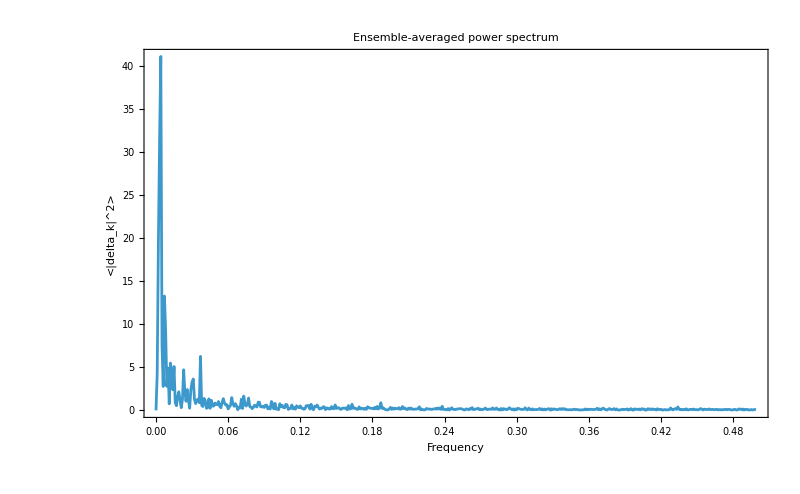

```mathematica
(*Ensemble-averaged length spectrum power*)
allPower=Table[FluctuationPowerSpectrum[GetFluctuations[qktEnsemble["Odd"][[i]]]]["Power"],{i,nReal}];
meanPower=Mean[allPower];
freqs=FluctuationPowerSpectrum[GetFluctuations[qktEnsemble["Odd"][[1]]]]["Freq"];

ListLinePlot[Transpose[{freqs,meanPower}],PlotRange->All,$pOpts,FrameLabel->{"Frequency","<|delta_k|^2>"},PlotLabel->"Ensemble-averaged power spectrum"]
```

# Gof

```mathematica
(* ================================================================ *)
(* MODULE 9: GoF ERRORS (parallelized per realization)              *)
(* ================================================================ *)

Print["\n=== GoF PER REALIZATION ==="];
DistributeDefinitions[ComputeGoFSingle, NNSpacings, IntWignerCOE, IntPrCOEFast,
  KSFromSorted, CvMFromSorted, MSDFromSorted];

{tE, gofEvenAll} = AbsoluteTiming[
  ParallelTable[ComputeGoFSingle[qktEnsemble["Even"][[i]]],
    {i, nReal}, Method -> "CoarsestGrained"]];
{tO, gofOddAll} = AbsoluteTiming[
  ParallelTable[ComputeGoFSingle[qktEnsemble["Odd"][[i]]],
    {i, nReal}, Method -> "CoarsestGrained"]];
Print["  Even: ", Round[tE, 0.1], "s, Odd: ", Round[tO, 0.1], "s"];

labels = {"KS_s", "CvM_s", "MSD_s", "KS_r", "CvM_r", "MSD_r"};
Do[
  Print["  ", labels[[idx]], ": Even mean=",
    NumberForm[Mean[gofEvenAll[[All, idx]]], 4],
    ", Odd mean=", NumberForm[Mean[gofOddAll[[All, idx]]], 4]];
, {idx, 6}];

(* Histograms *)
Do[
  Module[{eV = gofEvenAll[[All, idx]], oV = gofOddAll[[All, idx]]},
    SavePlot[Legended[Show[
      Histogram[{eV, oV}, Automatic, "ProbabilityDensity",
        ChartStyle -> {Directive[Blue, Opacity[0.5]], Directive[Darker[Green], Opacity[0.5]]}],
      $pOpts, FrameLabel -> {labels[[idx]], "Density"},
      PlotLabel -> labels[[idx]] <> " distribution (" <> ToString[nReal] <> " realizations)"],
      Placed[LineLegend[{Directive[Blue, Opacity[0.5]], Directive[Darker[Green], Opacity[0.5]]},
        {"Even", "Odd"}, LabelStyle -> $legStyle], {Right, Top}]
    ], "gof_" <> labels[[idx]]]];
, {idx, 6}];

Export[FileNameJoin[{evenDir, "gof.wdx"}], gofEvenAll, "WDX"];
Export[FileNameJoin[{oddDir, "gof.wdx"}], gofOddAll, "WDX"];
```

=== GoF PER REALIZATION ===

Even: 0.2s, Odd: 0.s

KS_s: Even mean=0.03284, Odd mean=0.04245

CvM_s: Even mean=0.0004414, Odd mean=0.000467

MSD_s: Even mean=0.0002857, Odd mean=0.0003093

KS_r: Even mean=0.05122, Odd mean=0.03875

CvM_r: Even mean=0.0009575, Odd mean=0.0005199

MSD_r: Even mean=0.0008184, Odd mean=0.0003759

Saved: gof_KS_s.png

Saved: gof_CvM_s.png

Saved: gof_MSD_s.png

Saved: gof_KS_r.png

Saved: gof_CvM_r.png

Saved: gof_MSD_r.png

# SFF

```mathematica
EnsembleSFFFull[spectraList_List,tauMax_Real,nPts_Integer]:=Module[{nMat,taus,specArray,allK},nMat=Length[spectraList];
taus=N[Range[1,nPts] (tauMax/nPts)];
specArray=Map[#["Spectrum"]&,spectraList];
DistributeDefinitions[CompileSFF,taus,specArray];
allK=ParallelTable[CompileSFF[specArray[[i]],taus],{i,nMat},Method->"CoarsestGrained"];
<|"Tau"->taus,"AllK"->allK,"MeanK"->Mean[allK],"SE"->StandardDeviation[allK]/Sqrt[nMat*1.]|>];
SmoothSFF[kVec_List,tauVec_List,sigmaTau_?NumericQ]:=GaussianFilter[kVec,sigmaTau/(tauVec[[2]]-tauVec[[1]])];
```

## method

```mathematica
tauMaxSFF=3.0;
nPtsSFF=10000;
sigmaSm=0.01;

sffEven=EnsembleSFFFull[qktEnsemble["Even"],tauMaxSFF,nPtsSFF];
sffOdd=EnsembleSFFFull[qktEnsemble["Odd"],tauMaxSFF,nPtsSFF];
sffCOE=EnsembleSFFFull[coeSpectra,tauMaxSFF,nPtsSFF];

tauGrid=sffEven["Tau"];

(*Smooth each realization individually,then take the mean of the smoothed curves*)
kEvenAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffEven["AllK"]];
kOddAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffOdd["AllK"]];
kCOEAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffCOE["AllK"]];

kEvenMeanSm=Mean[kEvenAllSm];
kOddMeanSm=Mean[kOddAllSm];
kCOEMeanSm=Mean[kCOEAllSm];

kCOEAn=Map[COESFFAnalytical,tauGrid];
```

## plotting

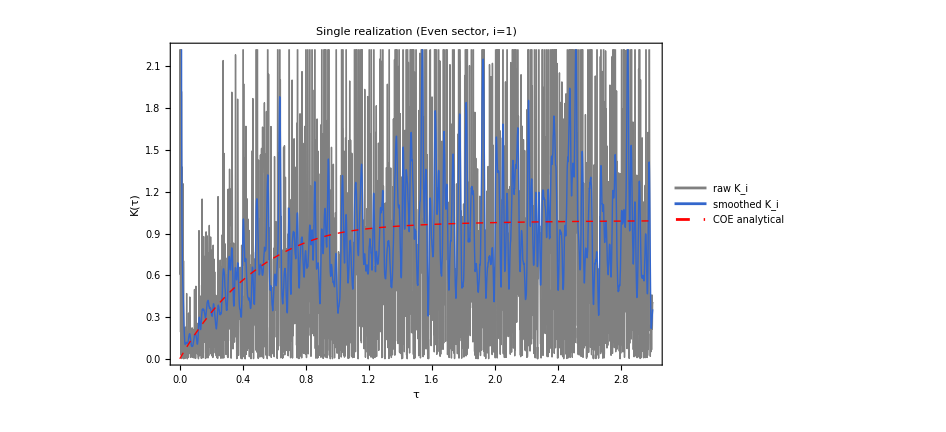

```mathematica
(*Pick one representative realization for the "individual" panel*)
iShow=1;

plotIndiv=ListLinePlot[{Transpose[{tauGrid,sffEven["AllK"][[iShow]]}],Transpose[{tauGrid,kEvenAllSm[[iShow]]}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"raw K_i","smoothed K_i","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Single realization (Even sector, i="<>ToString[iShow]<>")",ImageSize->700]
```

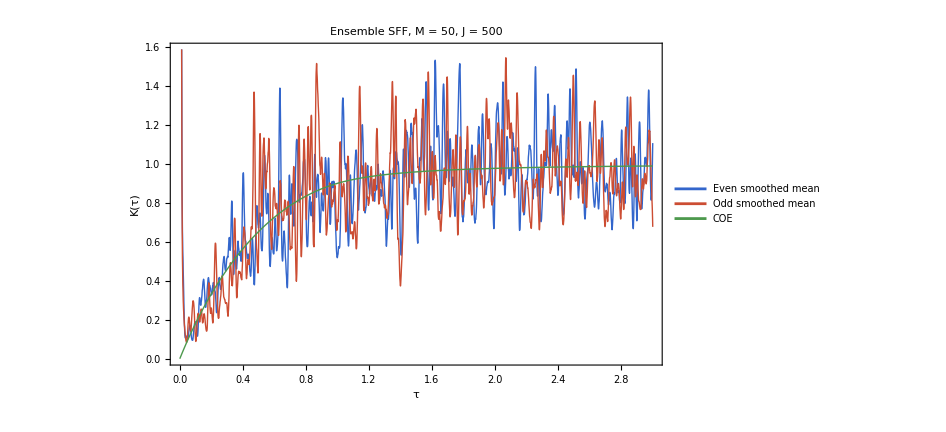

```mathematica
plotEnsemble=ListLinePlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

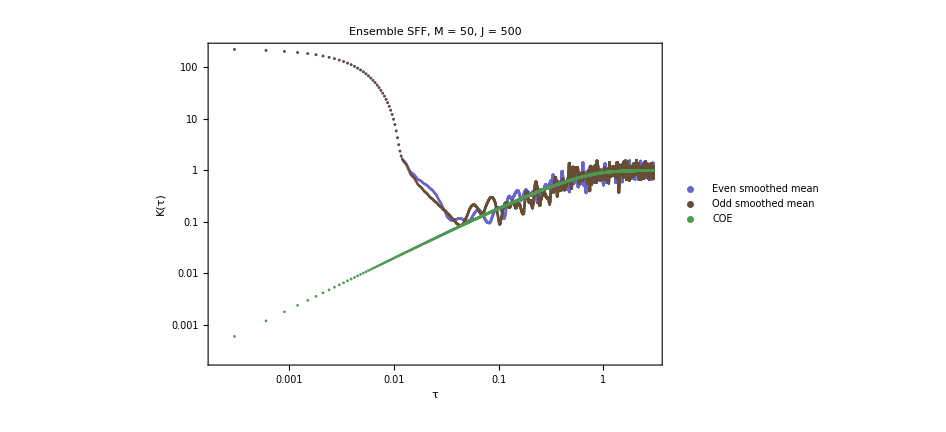

```mathematica
plot400=ListLogLogPlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.4,0.4,0.8]],Directive[Thick,RGBColor[0.4,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

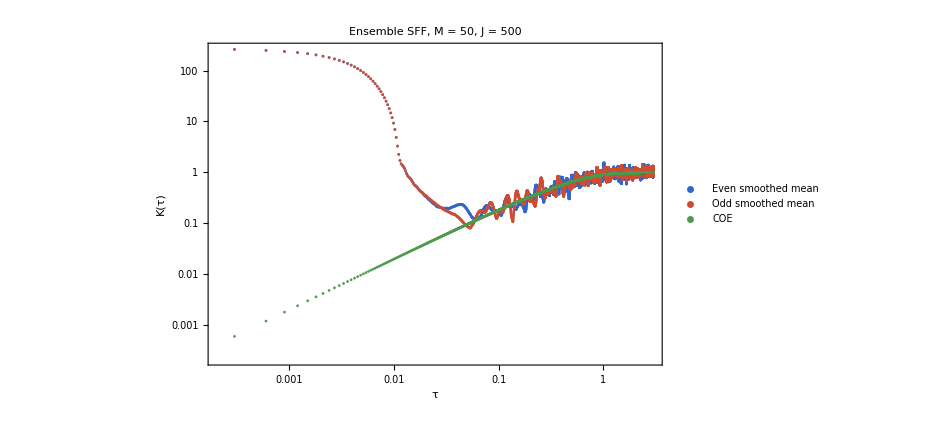

```mathematica
plot500=ListLogLogPlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

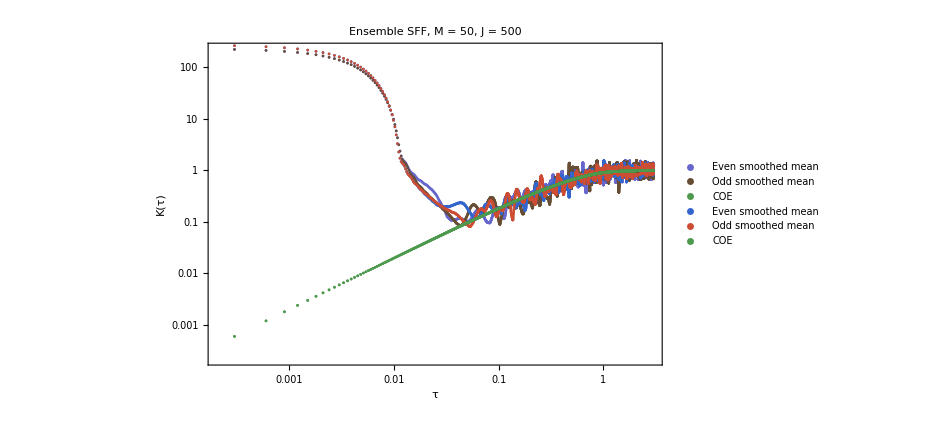

```mathematica
Show[plot400,plot500]
```

# Texture

```mathematica
TexturelessState[d_]:=TexturelessState[d]=N@ConstantArray[1/Sqrt[d],d];
```

```mathematica
(*Floquet parameters*)
J=400;
α=0.84;
k=27.5;
```

```mathematica
(*Generates all J operators, Jx, Jy, Jz, Jx^2*)
ops=generateSpinOperators[J];
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
```

```mathematica
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{neweigenvecM,neweigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.529326,0.535121}

```mathematica
f1=TexturelessState[J+1];
```

```mathematica
Clear[pk];
pk[k_]:=Abs[ConjugateTranspose[f1].neweigenvecM[[k]]]^2
```

```mathematica
phases=Arg[eigenvalM];
```

```mathematica
Clear[tex];
tex[t_]:=(J+1)Sum[pk[k]*pk[l]*Exp[-I*t(phases[[k]]-phases[[l]])],{k,J+1},{l,J+1}];
```

```mathematica
tlist=Range[0,100];
```

```mathematica
data=ParallelTable[tex[t],{t,tlist},Method->"CoarsestGrained"];
```

$Aborted

```mathematica
(*1. Define your initial state*)
f1=TexturelessState[J+1];
phases=Arg[eigenvalM];

(*2. PRECOMPUTE ALL OVERLAPS ONCE*)
(*Since neweigenvecM has eigenvectors as rows,matrix-vector multiplication gives us all dot products instantly.*)
pArray=Abs[neweigenvecM.f1]^2;

(*3. DEFINE THE VECTORIZED O(N) FUNCTION*)
Clear[texFast];
texFast[t_]:=(J+1)*Abs[Total[pArray*Exp[-I*t*phases]]]^2;
```

```mathematica
(*4. COMPUTE ACROSS TIME*)
tlist=Range[0,100];
```

```mathematica
(*You can use ParallelTable,but standard Table will likely finish in milliseconds now*)
AbsoluteTiming[data=Table[{t,texFast[t]},{t,tlist}];]
```

{0.001351,Null}

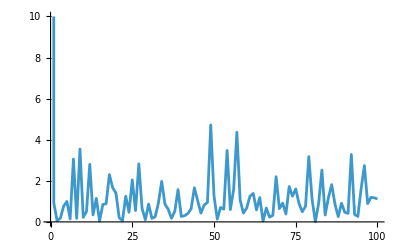

```mathematica
ListPlot[data,PlotRange->{All,{0,10}},Joined->True]
```

```mathematica
(* ================================================================*)(*1. SETUP& GENERATE DATA FOR ONE REALIZATION*)(* ================================================================*)
J=400;
alpha=0.84;
kCenter=27.5;

Print["Generating Eigensystem..."];
(*Assuming this function returns an association with "Even" and "Odd" sectors*)
data=GetQKTParityEigensystem[J,alpha,kCenter];

(*Extract data for the Even sector*)
eigenvalM=data["Even","Quasienergies"];
neweigenvecM=data["Even","Vectors"];
```

Generating Eigensystem...

```mathematica
(* ================================================================*)
(*2. PRECOMPUTE OVERLAPS*)
(* ================================================================*)
Print["Precomputing overlaps..."];
phases=Arg[eigenvalM];
d=Length[phases]; (*Dimension of this specific parity sector*)

(*Create the textureless state for the correct dimension*)
f1=N@ConstantArray[1/Sqrt[d],d];

(*Calculate all overlap probabilities instantly using matrix math*)
pArray=Abs[neweigenvecM.f1]^2;
```

Precomputing overlaps...

```mathematica
(* ================================================================*)
(*3. COMPUTE SURVIVAL PROBABILITY ACROSS TIME*)
(* ================================================================*)
tMax=1000; (*Evaluate up to 100 integer kicks*)
Print["Computing tex[t] over time..."];

(*The optimized O(N) function*)
Clear[texFast];
texFast[t_]:=d*Abs[Total[pArray*Exp[-I*t*phases]]]^2;

(*Generate the integer time grid and calculate the data*)
tGrid=Range[0,tMax];
texData=Table[texFast[t],{t,tGrid}];

Print["Data generated! Plotting..."];
```

Computing tex[t] over time...

Data generated! Plotting...

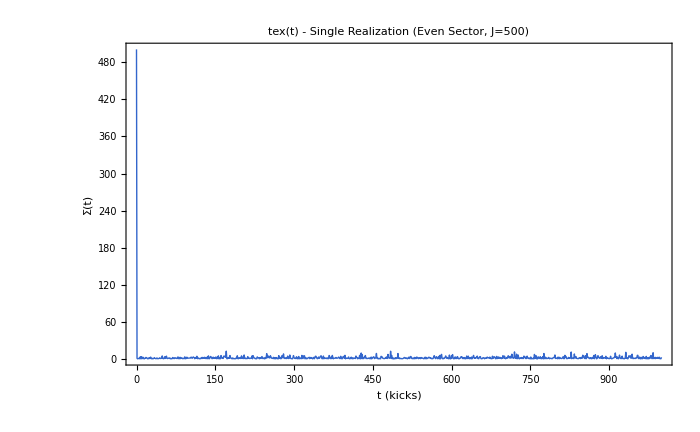

```mathematica
(* ================================================================*)
(*4. PLOT THE RESULT*)
(* ================================================================*)
plotTexSingle=ListLinePlot[Transpose[{tGrid,texData}],PlotRange->All,PlotStyle->Directive[Thick,RGBColor[0.2,0.4,0.8]],Frame->True,FrameLabel->{"t (kicks)","Σ(t)"},PlotLabel->"tex(t) - Single Realization (Even Sector, J="<>ToString[J]<>")",ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

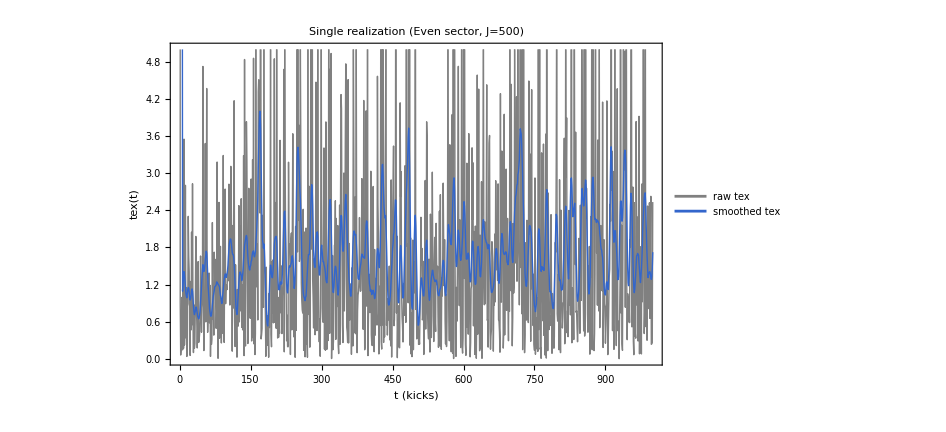

```mathematica
(* ================================================================*)(*SMOOTHING& PLOTTING FOR A SINGLE REALIZATION*)(* ================================================================*)(*Define smoothing window (e.g.,2 to 5 kicks for a 100-kick plot)*)
sigmaSm=5;

(*Apply Gaussian smoothing directly to the 1D list*)
texDataSmoothed=GaussianFilter[texData,sigmaSm];

(*Plot matching your exact SFF style*)
plotIndivTex=ListLinePlot[{Transpose[{tGrid,texData}],Transpose[{tGrid,texDataSmoothed}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]]},PlotLegends->{"raw tex","smoothed tex"},Frame->True,FrameLabel->{"t (kicks)","tex(t)"},PlotLabel->"Single realization (Even sector, J="<>ToString[J]<>")",ImageSize->700]
```

```mathematica
ClearAll["Global`*"];
(*1. Parameters*)
J=400;
α=0.84;
k=27.5;
Print["Generating Eigensystem..."];
(*2. Run your generator function*)
data=GetQKTParityEigensystem[J,α,k];
(*3. Extract Even sector data*)
eigenvalM=data["Even","Quasienergies"];
neweigenvecM=data["Even","Vectors"];
(*4. SANITY CHECKS*)
Print["Type of Quasienergies: ",Head[eigenvalM]];
Print["Dimensions of Vectors: ",Dimensions[neweigenvecM]];
```

Generating Eigensystem...

Type of Quasienergies: List

Dimensions of Vectors: {501,501}

```mathematica
(*1. Setup the state*)
phases=Arg[eigenvalM];
d=Length[phases];
f1=N@ConstantArray[1/Sqrt[d],d];

Print["Precomputing overlaps..."];
(*2. Calculate the physical overlaps*)
pArray=Abs[neweigenvecM.f1]^2;

(*SANITY CHECK*)
Print["Dimensions of pArray: ",Dimensions[pArray]];
Print["First 3 elements of pArray: ",Take[pArray,3]];
```

Precomputing overlaps...

Dimensions of pArray: {501}

First 3 elements of pArray: {0.000258918,0.00361785,0.000837065}

Computing time evolution...

Plotting...

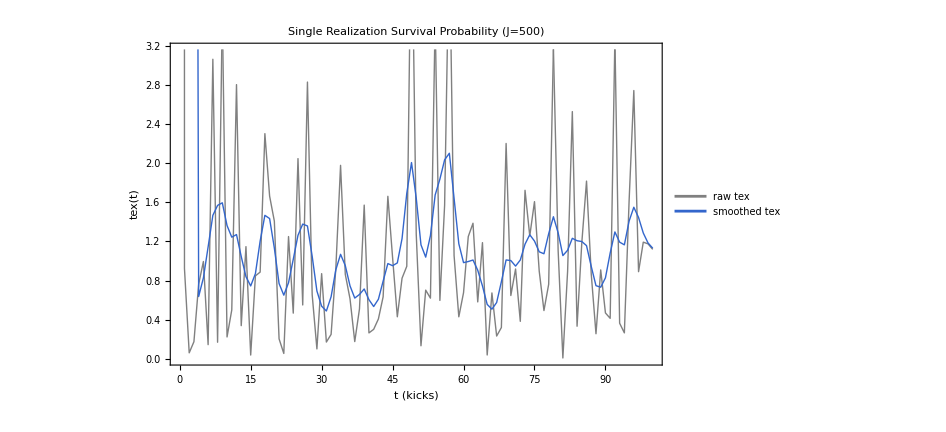

```mathematica
(*1. Setup Time Grid*)
tMax=100;
tGrid=Range[0,tMax];

(*2. Define Fast tex[t] function*)
Clear[texFast];
texFast[t_]:=d*Abs[Total[pArray*Exp[-I*t*phases]]]^2;

Print["Computing time evolution..."];
(*3. Generate the data*)
texData=Table[texFast[t],{t,tGrid}];

(*4. Smooth the data (3-kick window)*)
sigmaSm=3;
texDataSmoothed=GaussianFilter[texData,sigmaSm];

Print["Plotting..."];
(*5. Plot the result*)
plotIndivTex=ListLinePlot[{Transpose[{tGrid,texData}],Transpose[{tGrid,texDataSmoothed}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]]},PlotLegends->{"raw tex","smoothed tex"},Frame->True,FrameLabel->{"t (kicks)","tex(t)"},PlotLabel->"Single Realization Survival Probability (J="<>ToString[J]<>")",ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

```mathematica
(* ================================================================*)(*1. DEFINE THE ENSEMBLE FUNCTION*)(* ================================================================*)EnsembleTexFull[ensembleList_List,tMax_Integer]:=Module[{nMat,tGrid,allTex},
nMat=Length[ensembleList];
tGrid=Range[0,tMax];(*Integer time grid*)
Print["Processing ",nMat," realizations up to t = ",tMax,"..."];
(*Distribute the grid to parallel kernels*)
DistributeDefinitions[tGrid];
allTex=ParallelTable[Module[{phases,vecs,d,f1,pArray},(*Extract data for realization'i'*)
phases=ensembleList[[i,"Phases"]];
vecs=ensembleList[[i,"Vectors"]];
d=Length[phases];
(*Textureless state& Overlaps*)
f1=N@ConstantArray[1/Sqrt[d],d];
(*pArray=Abs[vecs.f1]^2;*)
pArray=Abs[vecs.f1]^2;
(*Fast O(N) evaluation*)
Table[d*Abs[Total[pArray*Exp[-I*t*phases]]]^2,{t,tGrid}]],{i,nMat},Method->"CoarsestGrained"];
(*Return the structured data*)<|"Time"->tGrid,"AllTex"->allTex,"MeanTex"->Mean[allTex]|>];
```

```mathematica
(*1. Setup Parameters*)
nQKT=50;
J=400;
α=0.84;
kCenter=10.0;
δ=0.05; (*Adjust your kick perturbation window if needed*)

(*Generate 100 slightly different kick strengths*)
kList=RandomReal[{kCenter-δ,kCenter+δ},nQKT];

Print["Generating ",nQKT," matrices. This might take a moment..."];

(*2. Generate all 100 eigensystems in parallel*)
rawEnsembleData=ParallelTable[GetQKTParityEigensystem[J,α,k],{k,kList},Method->"CoarsestGrained"];

Print["Packing data into qktEnsemble..."];

(*3. Structure the data correctly with both Phases and Vectors*)
qktEnsemble=<|"Even"->Table[<|"Phases"->Arg[data["Even","Quasienergies"]],"Vectors"->data["Even","Vectors"]|>,{data,rawEnsembleData}],"Odd"->Table[<|"Phases"->Arg[data["Odd","Quasienergies"]],"Vectors"->data["Odd","Vectors"]|>,{data,rawEnsembleData}]|>;

Print["Done! Checking ensemble size..."];
Print["Length of Even Ensemble: ",Length[qktEnsemble["Even"]]];
```

Generating 50 matrices. This might take a moment...

Packing data into qktEnsemble...

Done! Checking ensemble size...

Length of Even Ensemble: 50

```mathematica
qktEnsemble=<|"Even"->Table[<|"Phases"->Arg[data["Even","Quasienergies"]],"Vectors"->data["Even","Vectors"]|>,{data,rawEnsembleData}],"Odd"->Table[<|"Phases"->Arg[data["Odd","Quasienergies"]],"Vectors"->data["Odd","Vectors"]|>,{data,rawEnsembleData}]|>;
```

```mathematica
Table[{val,vec}=Eigensystem[RandomVariate[GaussianOrthogonalMatrixDistribution[J]]],
<|"Phases"->Arg[data["Even","Quasienergies"]],"Vectors"->data["Even","Vectors"]|>,{data,rawEnsembleData}]
```

```mathematica
(* ================================================================*)(*1. COMPUTE THE ENSEMBLE AVERAGE (using your matrices)*)(* ================================================================*)
tMaxTex=1000; (*Number of integer kicks to compute*)
sigmaSm=5;   (*Gaussian smoothing window size in kicks*)

Print["Computing Even Sector..."];
texEven=EnsembleTexFull[qktEnsemble["Even"],tMaxTex];

Print["Computing Odd Sector..."];
texOdd=EnsembleTexFull[qktEnsemble["Odd"],tMaxTex];

tGrid=texEven["Time"];
```

Computing Even Sector...

Processing 50 realizations up to t = 1000...

Computing Odd Sector...

Processing 50 realizations up to t = 1000...

Smoothing data...

Generating Plots...

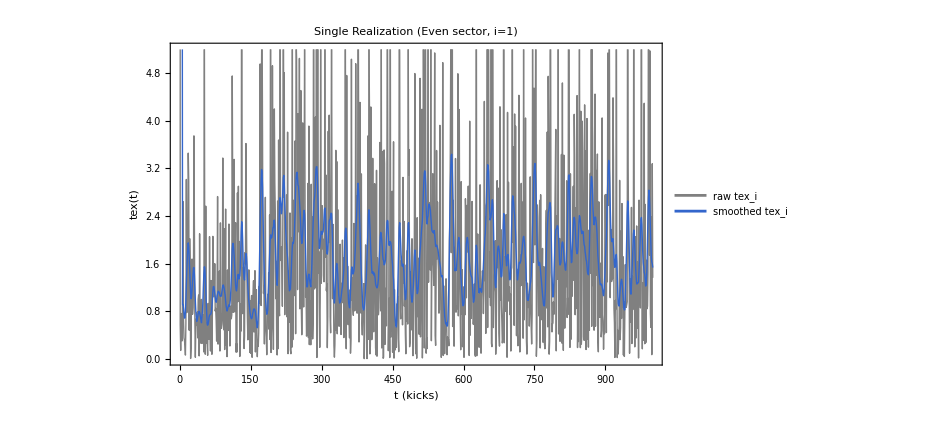

```mathematica
(* ================================================================*)
(*2. SMOOTH THE DATA*)
(* ================================================================*)

Print["Smoothing data..."];

(*Smooth each realization individually*)
texEvenAllSm=Map[GaussianFilter[#,sigmaSm]&,texEven["AllTex"]];
texOddAllSm=Map[GaussianFilter[#,sigmaSm]&,texOdd["AllTex"]];

(*Compute the ensemble mean of the smoothed curves*)
texEvenMeanSm=Mean[texEvenAllSm];
texOddMeanSm=Mean[texOddAllSm];


(* ================================================================*)
(*3. PLOT THE RESULTS*)
(* ================================================================*)

Print["Generating Plots..."];

(*---Plot 1:Individual Realization (Realization #1 out of 20)---*)
iShow=1;
plotIndivTex=ListLinePlot[{Transpose[{tGrid,texEven["AllTex"][[iShow]]}],Transpose[{tGrid,texEvenAllSm[[iShow]]}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]]},PlotLegends->{"raw tex_i","smoothed tex_i"},Frame->True,FrameLabel->{"t (kicks)","tex(t)"},PlotLabel->"Single Realization (Even sector, i="<>ToString[iShow]<>")",ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]];

Print[plotIndivTex];
```

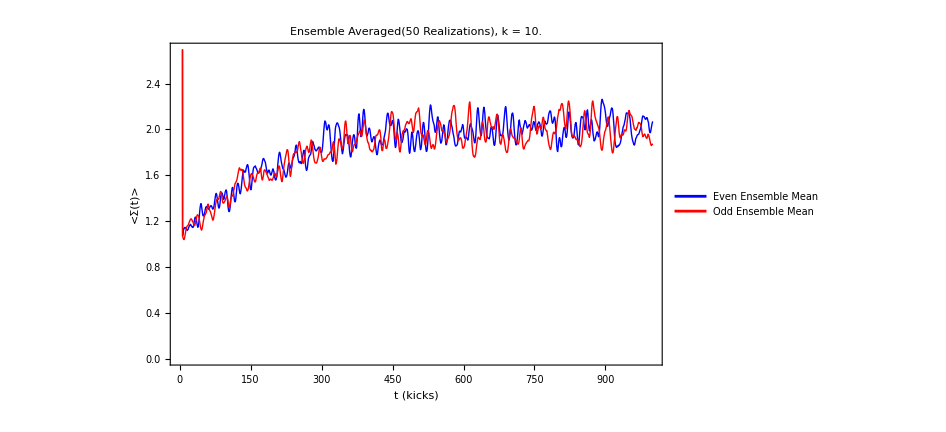

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = "<>ToString[kCenter],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

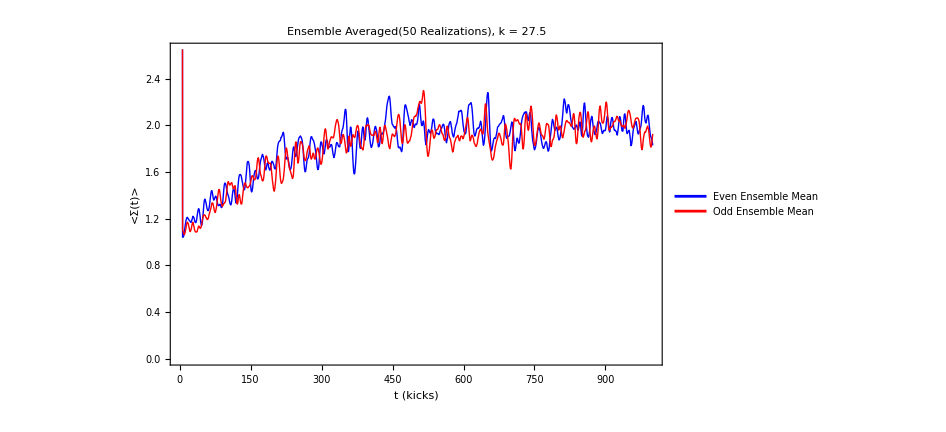

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = "<>ToString[k],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = "<>ToString[k],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

-Graphics-

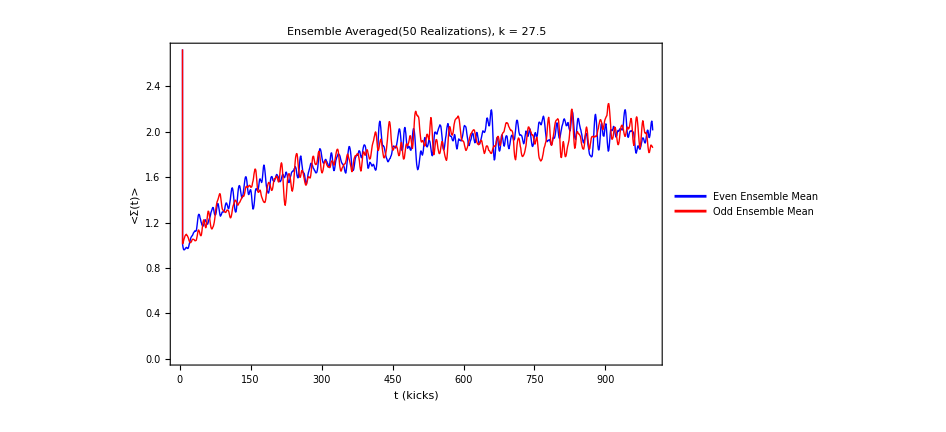

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = 27.5",ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

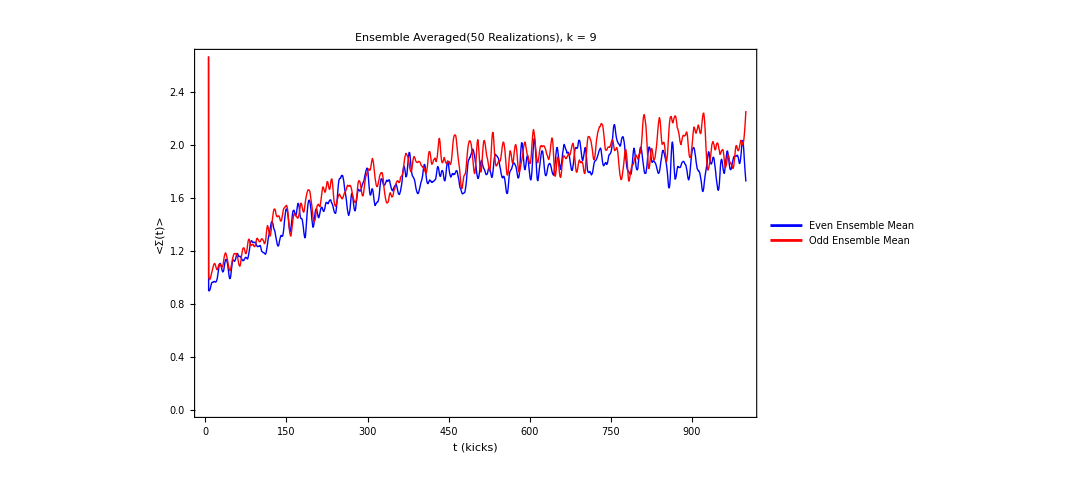

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = 9",ImageSize->800,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

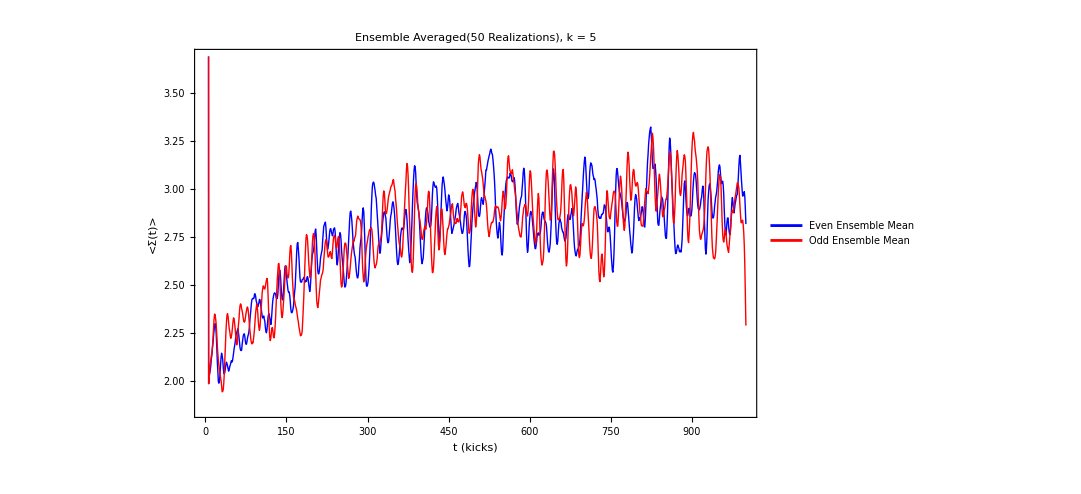

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = 5",ImageSize->800,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

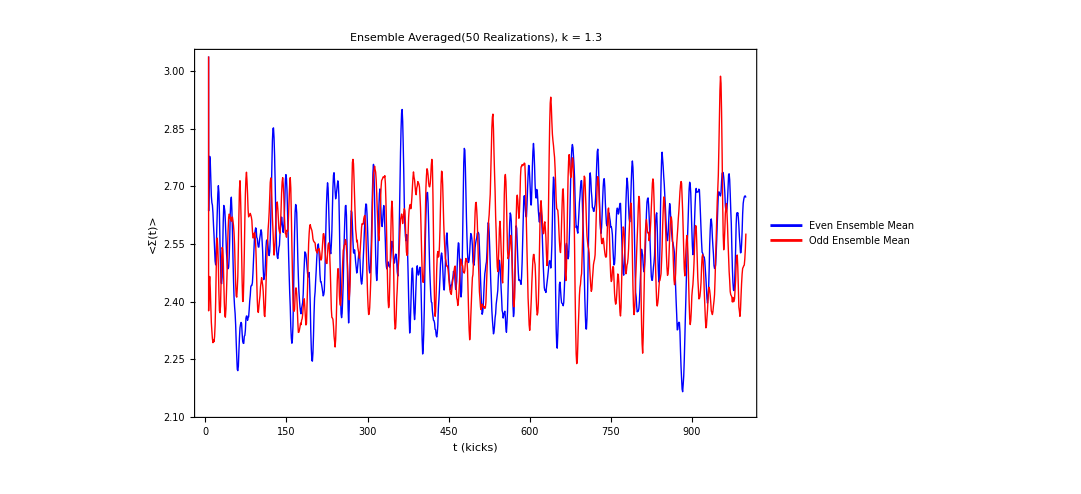

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged(50 Realizations), k = 1.3",ImageSize->800,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

## adfad

```mathematica
(* ================================================================ *)
(* 1. SETUP PARAMETERS FOR COE                                      *)
(* ================================================================ *)
nMat = 50;    (* Number of realizations / matrices *)
dim = 400;    (* Matrix dimension (Matches J/2 for J=400) *)

Print["Generating ", nMat, " COE matrices of dimension ", dim, "..."];

(* 2. Generate Eigensystems directly from Random Matrix Theory *)
coeEnsembleData = ParallelTable[
  Module[{mat, vals, vecs},
    
    (* Draw a random symmetric unitary matrix from the COE *)
    mat = RandomVariate[CircularOrthogonalMatrixDistribution[dim]];
    
    (* Compute the eigensystem *)
    {vals, vecs} = Eigensystem[mat];
    
    (* Structure it exactly how EnsembleTexFull expects it *)
    <|
      "Phases" -> Arg[vals], 
      "Vectors" -> vecs
    |>
  ],
  {nMat},
  Method -> "CoarsestGrained"
];

Print["Done! Length of COE Ensemble: ", Length[coeEnsembleData]];
```

Generating 50 COE matrices of dimension 400...

Done! Length of COE Ensemble: 50

```mathematica
(* ================================================================ *)
(* 3. COMPUTE THE ENSEMBLE AVERAGE (COE)                            *)
(* ================================================================ *)

tMaxTex = 1000; (* Number of integer kicks to compute *)
sigmaSm = 5;   (* Gaussian smoothing window size in kicks *)

Print["Computing COE Survival Probability..."];
texCOE = EnsembleTexFull[coeEnsembleData, tMaxTex];

tGrid = texCOE["Time"];

(* ================================================================ *)
(* 4. SMOOTH THE DATA                                               *)
(* ================================================================ *)
Print["Smoothing data..."];

(* Smooth each realization individually *)
texCOEAllSm = Map[GaussianFilter[#, sigmaSm] &, texCOE["AllTex"]];

(* Compute the ensemble mean of the smoothed curves *)
texCOEMeanSm = Mean[texCOEAllSm];
```

Computing COE Survival Probability...

Processing 50 realizations up to t = 1000...

Smoothing data...

Generating Plots...

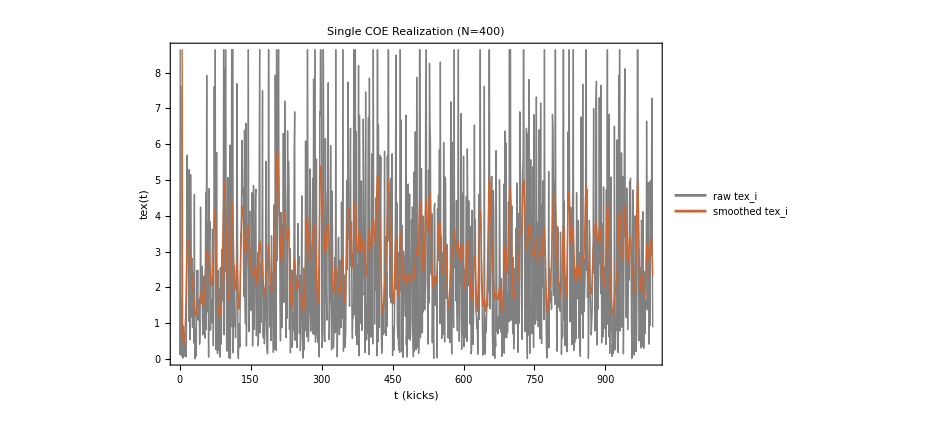

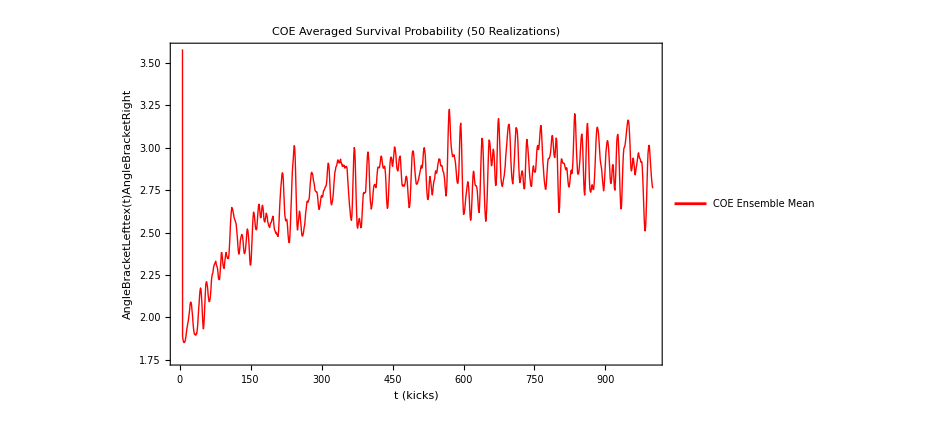

```mathematica
(* ================================================================ *)
(* 5. PLOT THE RESULTS                                              *)
(* ================================================================ *)
Print["Generating Plots..."];

(* --- Plot 1: Individual COE Realization --- *)
iShow = 1;
plotIndivCOE = ListLinePlot[
  {
    Transpose[{tGrid, texCOE["AllTex"][[iShow]]}], 
    Transpose[{tGrid, texCOEAllSm[[iShow]]}]
  },
  PlotStyle -> {
    Directive[Thin, Gray], 
    Directive[Thick, RGBColor[0.8, 0.4, 0.2]] (* Using Orange/Red for COE *)
  },
  PlotLegends -> {"raw tex_i", "smoothed tex_i"},
  Frame -> True, 
  FrameLabel -> {"t (kicks)", "tex(t)"},
  PlotLabel -> "Single COE Realization (N=" <> ToString[dim] <> ")",
  ImageSize -> 700,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]
];

(* --- Plot 2: COE Ensemble Average --- *)
plotMeanCOE = ListLinePlot[
  Transpose[{tGrid, texCOEMeanSm}],
  PlotStyle -> Directive[Thick, Red],
  PlotLegends -> Placed[LineLegend[{"COE Ensemble Mean"}], {0.85, 0.15}],
  Frame -> True,
  FrameLabel -> {"t (kicks)", "\!\(\*AngleBracketLeft\)tex(t)\!\(\*AngleBracketRight\)"},
  PlotLabel -> "COE Averaged Survival Probability (" <> ToString[nMat] <> " Realizations)",
  ImageSize -> 700,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]
];

Print[plotIndivCOE];
Print[plotMeanCOE];
```